# Angular Crossing Collimated Flux

## Units + Constants

```mathematica
(*Units*)
MeV=10^6;
keV=10^3;
nC=10^-9;
pC=10^-12;
μJ=10^-6;
nm=10^-9;
mrad=10^-3;
mm=10^-3;
cm=10^-2;
μm=10^-6;
MHz=10^6;
ps=10^-12;
```

```mathematica
(*Constants*)
σT=6.65245871548*10^-29;
re=2.8179403262*10^-15;
clight=299792458;
hbar=6.5821*10^-16; (*converted to eV, wavelength calc changed accordingly*)
me=0.51099895MeV; (*mc^2 really*)
elecharge=1.60217662*10^-19;
```

```mathematica
(*Angles*)
fivedeg=(5*π)/180;
```

## Plotting

```mathematica
frame[legend_]:=Framed[legend,FrameStyle->Black,RoundingRadius->0,FrameMargins->0]
```

## Cases

The optimised values within these cases are using the Compton_Optimisation_Parrallel.nb code, which is outdated (doesn’t include hourglass effect), but is the best for comparing to spectra etc.

```mathematica
headonCBETA150={Ee->150MeV,ϕ->0,λ->1064nm,Q->32pC,Epulse->62μJ,βIP->1cm,ϵn->0.3mm mrad,σL->25μm,σze->1mm,tpulse->10ps,f->162.5MHz,θcol->0.5mrad};
headonCBETA150opt={Ee->150MeV,ϕ->0,λ->1064nm,Q->32pC,Epulse->62μJ,βIP->12.6189cm,ϵn->0.3mm mrad,σL->25μm,σze->1mm,tpulse->10ps,f->162.5MHz,θcol->0.43333mrad};
CBETA150opt={Ee->150MeV,ϕ->fivedeg,λ->1064nm,Q->32pC,Epulse->62μJ,βIP->12.6189cm,ϵn->0.3mm mrad,σL->25μm,σze->1mm,tpulse->10ps,f->162.5MHz,θcol->0.43333mrad};

headonDIANA687={Ee->687MeV,ϕ->0,λ->1064nm,Q->100pC,Epulse->100μJ,βIP->0.2,ϵn->0.5mm mrad,σL->25 μm,σze->1mm,tpulse->5.7ps,f->100MHz,θcol->0.1mrad};
headonDIANA687opt={Ee->687MeV,ϕ->0,λ->1064nm,Q->100pC,Epulse->100μJ,βIP->0.603575,ϵn->0.5mm mrad,σL->25 μm,σze->1mm,tpulse->5.7ps,f->100MHz,θcol->0.09181mrad};
DIANA687opt={Ee->687MeV,ϕ->fivedeg,λ->1064nm,Q->100pC,Epulse->100μJ,βIP->0.603575,ϵn->0.5mm mrad,σL->25 μm,σze->1mm,tpulse->5.7ps,f->100MHz,θcol->0.09181mrad};
```

## Integrated Cross Section Calculation

## Intermediaries

```mathematica
(*Scattered photon energy equations*) 
γ[Ee_]:=(Ee+me)/me;
β[Ee_]:=Sqrt[1-1/γ[Ee]^2];
EL[λ_]:=(2*π*hbar*clight)/λ; (*in eV, using hbar*)
```

## Scattered Photon Energy

```mathematica
Eγ[Ee_,ϕ_,λ_,θ_]:=(EL[λ]*(1+β[Ee]*Cos[ϕ]))/(1-β[Ee]*Cos[θ]+EL[λ]/Ee*(1+Cos[ϕ+θ]));
```

```mathematica
Eγ[Ee,ϕ,λ,0]/.headonCBETA150
```

403281.

## Lorentz Invariants (from Mandelstam)

```mathematica
X[Ee_,ϕ_,λ_]:=(2γ[Ee]*EL[λ]*(1+β[Ee]*Cos[ϕ]))/me;
Y[Ee_,ϕ_,λ_,θ_]:=(2*γ[Ee]*Eγ[Ee,ϕ,λ,θ]*(1-β[Ee]*Cos[θ]))/me;
```

## Cross Section [Berestetskii, σ = f(Y)]

```mathematica
dσdY[Ee_,ϕ_,λ_,θ_]:=(8*π*re^2)/X[Ee,ϕ,λ]^2*((1/X[Ee,ϕ,λ]-1/Y[Ee,ϕ,λ,θ])^2+1/X[Ee,ϕ,λ]-1/Y[Ee,ϕ,λ,θ]+1/4*(X[Ee,ϕ,λ]/Y[Ee,ϕ,λ,θ]+Y[Ee,ϕ,λ,θ]/X[Ee,ϕ,λ]));
```

## Lorentz Invariant Y Differential [Me, Y = f(θ)]

```mathematica
dYdθ[Ee_,θ_,ϕ_,λ_]:=(X[Ee,ϕ,λ]*β[Ee]*Sin[θ]*(1-β[Ee]*Cos[θ]+(1+Cos[ϕ+θ])*EL[λ]/Ee)-X[Ee,ϕ,λ]*(1-β[Ee]*Cos[θ])*(β[Ee]*Sin[θ]-EL[λ]/Ee*Sin[ϕ+θ]))/(1-β[Ee]*Cos[θ]+(1+Cos[ϕ+θ])*EL[λ]/Ee)^2;
```

## Cross Section [Me, σ = f(θ)]

```mathematica
dσdθ[Ee_,ϕ_,λ_,θ_]:=dσdY[Ee,ϕ,λ,θ]*dYdθ[Ee,θ,ϕ,λ];
```

```mathematica
σ[Ee_,ϕ_,λ_,θcol_,case_]:=NIntegrate[dσdθ[Ee,ϕ,λ,θ]/.case,{θ,0,θcol/.case}];
```

## Integrated Cross Section Investigation

## Integrated Cross Section Plots

```mathematica
σvsθCBETA150=Table[{θ/mrad,σ[Ee,ϕ,λ,θ,headonCBETA150opt]/σT,σ[Ee,ϕ,λ,θ,CBETA150opt]/σT,σ[Ee,(45*π)/180,λ,θ,CBETA150opt]/σT,σ[Ee,(90*π)/180,λ,θ,CBETA150opt]/σT,σ[Ee,(270*π)/180,λ,θ,CBETA150opt]/σT},{θ,-1/γ[Ee]/.CBETA150opt,1/γ[Ee]/.CBETA150opt,1/(1000*γ[Ee])/.CBETA150opt}];
```

```mathematica
σvsθDIANA687=Table[{θ/mrad,σ[Ee,ϕ,λ,θ,headonDIANA687opt]/σT,σ[Ee,ϕ,λ,θ,DIANA687opt]/σT,σ[Ee,(45*π)/180,λ,θ,DIANA687opt]/σT,σ[Ee,(90*π)/180,λ,θ,DIANA687opt]/σT,σ[Ee,(270*π)/180,λ,θ,DIANA687opt]/σT},{θ,-1/γ[Ee]/.DIANA687opt,1/γ[Ee]/.DIANA687opt,1/(1000*γ[Ee])/.DIANA687opt}];
```

```mathematica
csCBETA150=ListLinePlot[{Partition[Riffle[σvsθCBETA150⟦All,1⟧,σvsθCBETA150⟦All,2⟧],2],Partition[Riffle[σvsθCBETA150⟦All,1⟧,σvsθCBETA150⟦All,3⟧],2],Partition[Riffle[σvsθCBETA150⟦All,1⟧,σvsθCBETA150⟦All,4⟧],2],Partition[Riffle[σvsθCBETA150⟦All,1⟧,σvsθCBETA150⟦All,5⟧],2],Partition[Riffle[σvsθCBETA150⟦All,1⟧,σvsθCBETA150⟦All,6⟧],2]},Frame->True,PlotStyle->{Red,Blue,Orange,Green,Purple},LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},PlotLabel->"CBETA 150 MeV",FrameLabel->{"Collimation Angle [mrad]","Norm. Int. Cross Section [σ/σ_T]"},PlotLegends->Placed[LineLegend[{"ϕ = 0°","ϕ = 5°","ϕ = 45°","ϕ = 90°","ϕ = 270°"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.15,0.2}],ImageSize->Large];
```

```mathematica
csDIANA687=ListLinePlot[{Partition[Riffle[σvsθDIANA687⟦All,1⟧,σvsθDIANA687⟦All,2⟧],2],Partition[Riffle[σvsθDIANA687⟦All,1⟧,σvsθDIANA687⟦All,3⟧],2],Partition[Riffle[σvsθDIANA687⟦All,1⟧,σvsθDIANA687⟦All,4⟧],2],Partition[Riffle[σvsθDIANA687⟦All,1⟧,σvsθDIANA687⟦All,5⟧],2],Partition[Riffle[σvsθDIANA687⟦All,1⟧,σvsθDIANA687⟦All,6⟧],2]},Frame->True,PlotStyle->{Red,Blue,Orange,Green,Purple},LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},PlotLabel->"DIANA 687 MeV",FrameLabel->{"Collimation Angle [mrad]","Norm. Int. Cross Section [σ/σ_T]"},PlotLegends->Placed[LineLegend[{"ϕ = 0°","ϕ = 5°","ϕ = 45°","ϕ = 90°","ϕ = 270°"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.15,0.2}],ImageSize->Large];
```

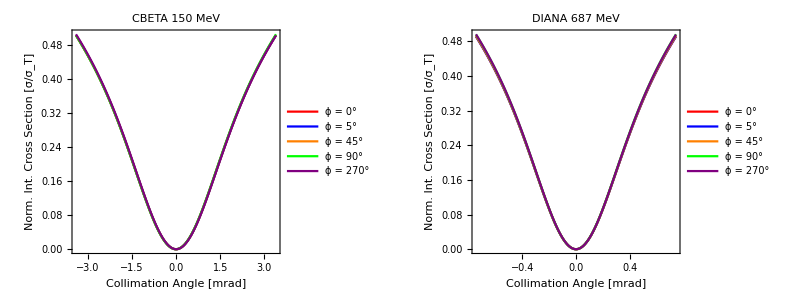

```mathematica
Grid[{{csCBETA150,csDIANA687}}]
```

## Integrated Cross Section Residuals

```mathematica
REScsCBETA150=ListLinePlot[{Partition[Riffle[σvsθCBETA150⟦All,1⟧,(σvsθCBETA150⟦All,2⟧-σvsθCBETA150⟦All,4⟧)*10^3],2],Partition[Riffle[σvsθCBETA150⟦All,1⟧,(σvsθCBETA150⟦All,2⟧-σvsθCBETA150⟦All,5⟧)*10^3],2],Partition[Riffle[σvsθCBETA150⟦All,1⟧,(σvsθCBETA150⟦All,2⟧-σvsθCBETA150⟦All,6⟧)*10^3],2]},Frame->True,LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},PlotLabel->"CBETA 150 MeV",FrameLabel->{"Collimation Angle [mrad]","Residual [(σ (0  °) - σ (ϕ))/σ_T ×10^-3]"},PlotLegends->Placed[LineLegend[{"ϕ = 45°","ϕ = 90°","ϕ = 270°"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.18,0.45}],ImageSize->Large];
```

```mathematica
REScsDIANA687=ListLinePlot[{Partition[Riffle[σvsθDIANA687⟦All,1⟧,(σvsθDIANA687⟦All,2⟧-σvsθDIANA687⟦All,4⟧)*10^3],2],Partition[Riffle[σvsθDIANA687⟦All,1⟧,(σvsθDIANA687⟦All,2⟧-σvsθDIANA687⟦All,5⟧)*10^3],2],Partition[Riffle[σvsθDIANA687⟦All,1⟧,(σvsθDIANA687⟦All,2⟧-σvsθDIANA687⟦All,6⟧)*10^3],2]},Frame->True,LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},PlotLabel->"DIANA 687 MeV",FrameLabel->{"Collimation Angle [mrad]","Residual [(σ (0  °) - σ (ϕ))/σ_T×10^-3]"},PlotLegends->Placed[LineLegend[{"ϕ = 45°","ϕ = 90°","ϕ = 270°"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.4,0.25}],ImageSize->Large];
```

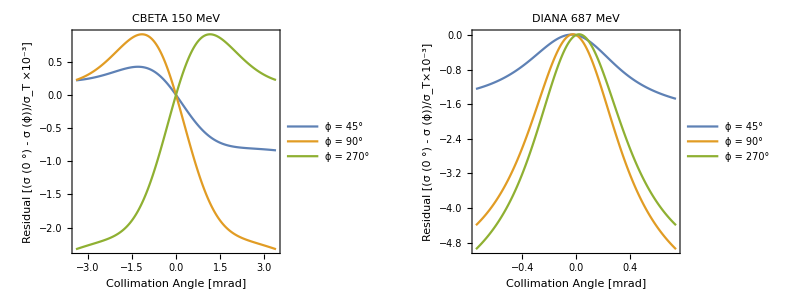

```mathematica
Grid[{{REScsCBETA150,REScsDIANA687}}]
```

## Collimated Flux Calculation